```mathematica
Clear[dis,dis2]
dis[j_,x_]:=dis[j,x]=dis[j-1,x]+j^(-1/2) (-1)^(j)N@Sin[x Log[j]]
dis[0,x_]:=0
dis2[j_,x_]:=dis2[j,x]=dis2[j-1,x]+j^(-1/2) N@Sin[x Log[j]]
dis2[0,x_]:=0
```

```mathematica
N@dis[20000,N@Im@ZetaZero@1]
```

0.00347674

```mathematica
$RecursionLimit = 10000000
```

10000000

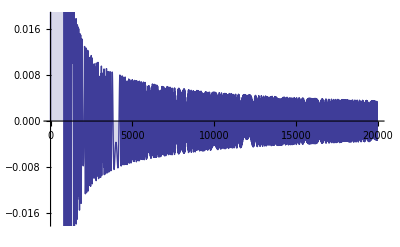

```mathematica
DiscretePlot[Re@dis[n,N@Im@ZetaZero@2000],{n,1,20000,10}]
```

```mathematica
FullSimplify[Sum[j^(-1/2) (-1)^(j)Sin[x Log[j]],{j,1,n}]]
```

-ⅈ 2^(-3/2-ⅈ x) (-Zeta[1/2+ⅈ x]+2^(2 ⅈ x) (Zeta[1/2-ⅈ x]-Zeta[1/2-ⅈ x,3/2]+(-1)^n (Zeta[1/2-ⅈ x,(1+n)/2]-Zeta[1/2-ⅈ x,(2+n)/2]))+Zeta[1/2+ⅈ x,3/2]-(-1)^n Zeta[1/2+ⅈ x,(1+n)/2]+(-1)^n Zeta[1/2+ⅈ x,(2+n)/2])

```mathematica
FullSimplify[Sum[ (-1)^(j)Sin[x Log[j]],{j,1,n}]]
```

-ⅈ 2^(-1-ⅈ x) (2^(ⅈ x) (-1+2^(1+ⅈ x)) Zeta[-ⅈ x]+(-2+2^(ⅈ x)) Zeta[ⅈ x]+(-1)^n (4^(ⅈ x) (Zeta[-ⅈ x,(1+n)/2]-Zeta[-ⅈ x,(2+n)/2])-Zeta[ⅈ x,(1+n)/2]+Zeta[ⅈ x,(2+n)/2]))

```mathematica
Limit[-ⅈ 2^(-3/2-ⅈ x) (-Zeta[1/2+ⅈ x]+2^(2 ⅈ x) (Zeta[1/2-ⅈ x]-Zeta[1/2-ⅈ x,3/2]+(-1)^n (Zeta[1/2-ⅈ x,(1+n)/2]-Zeta[1/2-ⅈ x,(2+n)/2]))+Zeta[1/2+ⅈ x,3/2]-(-1)^n Zeta[1/2+ⅈ x,(1+n)/2]+(-1)^n Zeta[1/2+ⅈ x,(2+n)/2]),n->Infinity]
```

Limit[-ⅈ 2^(-3/2-ⅈ x) (-Zeta[1/2+ⅈ x]+2^(2 ⅈ x) (Zeta[1/2-ⅈ x]-Zeta[1/2-ⅈ x,3/2]+(-1)^n (Zeta[1/2-ⅈ x,(1+n)/2]-Zeta[1/2-ⅈ x,(2+n)/2]))+Zeta[1/2+ⅈ x,3/2]-(-1)^n Zeta[1/2+ⅈ x,(1+n)/2]+(-1)^n Zeta[1/2+ⅈ x,(2+n)/2]),n→∞]

```mathematica
FullSimplify[Sum[j^(-1/2) (-1)^(j)Sin[x Log[j]],{j,1,Infinity}]]
```

∑_(j=1)^∞ ((-1)^j Sin[x Log[j]])/(√j)

```mathematica
Expand[FullSimplify[Sum[j^(-1/2) (-1)^(j)Sin[x Log[j]],{j,1,n}]/.x->Im@ZetaZero@2]]
```

ⅈ (-1)^n 2^(-2+ZetaZero[2]) Zeta[1-ZetaZero[2],1+n/2]-ⅈ (-1)^n 2^(-2+ZetaZero[2]) Zeta[1-ZetaZero[2],(1+n)/2]-ⅈ (-1)^n 2^(-1-ZetaZero[2]) Zeta[ZetaZero[2],1+n/2]+ⅈ (-1)^n 2^(-1-ZetaZero[2]) Zeta[ZetaZero[2],(1+n)/2]

```mathematica
N@Zeta[ZetaZero[1],60000]
```

17.3061-0.659029 ⅈ

```mathematica
FullSimplify[Sum[j^(-1/2) (-1)^(j)Cos[x Log[j]],{j,1,n}]]
```

2^(-3/2-ⅈ x) ((-2^(1/2+ⅈ x)+2^(1+2 ⅈ x)) Zeta[1/2-ⅈ x]-(-2+2^(1/2+ⅈ x)) Zeta[1/2+ⅈ x]+(-1)^n (2^(2 ⅈ x) (Zeta[1/2-ⅈ x,(1+n)/2]-Zeta[1/2-ⅈ x,(2+n)/2])+Zeta[1/2+ⅈ x,(1+n)/2]-Zeta[1/2+ⅈ x,(2+n)/2]))

```mathematica
Expand@FullSimplify@Sum[j^(-1/2) (-1)^(j)Sin[x Log[j]],{j,1,n}]
```

-ⅈ 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x]+ⅈ 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x]+ⅈ 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x,3/2]-ⅈ (-1)^n 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x,(1+n)/2]+ⅈ (-1)^n 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x,(2+n)/2]-ⅈ 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x,3/2]+ⅈ (-1)^n 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x,(1+n)/2]-ⅈ (-1)^n 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x,(2+n)/2]

```mathematica
fr[n_,x_]:={-ⅈ 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x],+ⅈ 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x],+ⅈ 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x,3/2],-ⅈ (-1)^n 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x,(1+n)/2],+ⅈ (-1)^n 2^(-3/2+ⅈ x) Zeta[1/2-ⅈ x,(2+n)/2],-ⅈ 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x,3/2],+ⅈ (-1)^n 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x,(1+n)/2],-ⅈ (-1)^n 2^(-3/2-ⅈ x) Zeta[1/2+ⅈ x,(2+n)/2]}
```

```mathematica
Chop@N@fr[100000000,.5]
```

{0.264488+0.268174 ⅈ,0.264488-0.268174 ⅈ,-0.216139-0.461478 ⅈ,-2974.74-1910.75 ⅈ,2974.74+1910.75 ⅈ,-0.216139+0.461478 ⅈ,-2974.74+1910.75 ⅈ,2974.74-1910.75 ⅈ}

```mathematica
N@Table[ sin[ Mod[N@Im@ZetaZero@100  Log[j],2Pi]],{j,1,200}]//TableForm
```

sin[0.]
sin[0.583285]
sin[2.23783]
sin[1.16657]
sin[3.67994]
sin[2.82111]
sin[1.58237]
sin[1.74985]
sin[4.47566]
sin[4.26323]
sin[1.67365]
sin[3.4044]
sin[3.48688]
sin[2.16566]
sin[5.91777]
sin[2.33314]
sin[4.10596]
sin[5.05894]
sin[5.28078]
sin[4.84651]
sin[3.8202]
sin[2.25694]
sin[0.204488]
sin[3.98768]
sin[1.0767]
sin[4.07017]
sin[0.430298]
sin[2.74894]
sin[4.7657]
sin[0.217871]
sin[1.69027]
sin[2.91642]
sin[3.91148]
sin[4.68925]
sin[5.26232]
sin[5.64223]
sin[5.83956]
sin[5.86406]
sin[5.72471]
sin[5.4298]
sin[4.98701]
sin[4.40348]
sin[3.68583]
sin[2.84022]
sin[1.87241]
sin[0.787773]
sin[5.87451]
sin[4.57097]
sin[3.16474]
sin[1.65999]
sin[0.0606035]
sin[4.65345]
sin[2.87563]
sin[1.01358]
sin[5.3536]
sin[3.33223]
sin[1.23542]
sin[5.34899]
sin[3.10905]
sin[0.801156]
sin[4.71074]
sin[2.27356]
sin[6.05803]
sin[3.49971]
sin[0.88364]
sin[4.49477]
sin[1.7684]
sin[5.27253]
sin[2.44232]
sin[5.8456]
sin[2.91743]
sin[6.22551]
sin[3.20478]
sin[0.139661]
sin[3.31453]
sin[0.164162]
sin[3.25603]
sin[0.0248087]
sin[3.0379]
sin[6.01308]
sin[2.66813]
sin[5.5703]
sin[2.15411]
sin[4.98677]
sin[1.50272]
sin[4.26912]
sin[0.720346]
sin[3.42351]
sin[6.09613]
sin[2.4557]
sin[5.06925]
sin[1.37106]
sin[3.9281]
sin[0.174611]
sin[2.67754]
sin[5.15425]
sin[1.32212]
sin[3.74803]
sin[6.14931]
sin[2.24327]
sin[4.59677]
sin[0.643888]
sin[2.95146]
sin[5.23674]
sin[1.21696]
sin[3.45891]
sin[5.67981]
sin[1.59687]
sin[3.77683]
sin[5.93688]
sin[1.7942]
sin[3.91551]
sin[6.01796]
sin[1.8187]
sin[3.88443]
sin[5.93227]
sin[1.67935]
sin[3.69234]
sin[5.68833]
sin[1.38444]
sin[3.34731]
sin[5.29402]
sin[0.941657]
sin[2.85684]
sin[4.75665]
sin[0.358127]
sin[2.22789]
sin[4.08299]
sin[5.92366]
sin[1.46693]
sin[3.27938]
sin[5.07805]
sin[0.579964]
sin[2.35169]
sin[4.11024]
sin[5.85582]
sin[1.30542]
sin[3.0256]
sin[4.73336]
sin[0.1457]
sin[1.82915]
sin[3.50071]
sin[5.16054]
sin[0.52561]
sin[2.16246]
sin[3.78806]
sin[5.40257]
sin[0.722946]
sin[2.31571]
sin[3.89782]
sin[5.46941]
sin[0.747447]
sin[2.29843]
sin[3.83931]
sin[5.37022]
sin[0.608094]
sin[2.11944]
sin[3.62118]
sin[5.11345]
sin[0.313183]
sin[1.78686]
sin[3.25141]
sin[4.70695]
sin[6.15358]
sin[1.30824]
sin[2.73739]
sin[4.15796]
sin[5.57005]
sin[0.690578]
sin[2.086]
sin[3.47325]
sin[4.8524]
sin[6.22356]
sin[1.30363]
sin[2.65907]
sin[4.00679]
sin[5.34688]
sin[0.396228]
sin[1.7213]
sin[3.03898]
sin[4.34937]
sin[5.65254]
sin[0.665379]
sin[1.95434]
sin[3.23632]
sin[4.51139]
sin[5.77962]
sin[0.757896]
sin[2.01267]
sin[3.26082]
sin[4.50242]
sin[5.73754]
sin[0.683052]
sin[1.9054]
sin[3.12147]
sin[4.33131]
sin[5.535]
sin[0.44941]
sin[1.64097]
sin[2.82656]

```mathematica
N@Mod[7,2Pi]
```

7.

```mathematica
Animate[DiscretePlot[ Mod[x  Log[j],2Pi],{j,1,500}],{x,100,103}]
```

```mathematica
Animate[DiscretePlot[ Sin[Mod[x  Log[j],2Pi]],{j,1,500}],{x,100,103}]
```

```mathematica
1/I
```

-ⅈ

```mathematica
(-I x(E^(I (x Log[n]+c))-E^(-I (x Log[n]+c)))+(1/2)(E^(I (x Log[n]+c))+E^(-I (x Log[n]+c))))(1/(j^(1/2)))(1/(2I))(E^(I (x Log[n]+c))-E^(-I (x Log[n]+c)))
```

-(ⅈ (-ⅇ^(-ⅈ (c+x Log[n]))+ⅇ^(ⅈ (c+x Log[n]))) (1/2 (ⅇ^(-ⅈ (c+x Log[n]))+ⅇ^(ⅈ (c+x Log[n])))-ⅈ (-ⅇ^(-ⅈ (c+x Log[n]))+ⅇ^(ⅈ (c+x Log[n]))) x))/(2 √j)

```mathematica
( x(E^(I (x Log[n]+c))+E^(-I (x Log[n]+c)))+(1/(2 I))(E^(I (x Log[n]+c))-E^(-I (x Log[n]+c))))(1/(j^(1/2)))(1/(2))(E^(I (x Log[n]+c))+E^(-I (x Log[n]+c)))
```

((ⅇ^(-ⅈ (c+x Log[n]))+ⅇ^(ⅈ (c+x Log[n]))) (-1/2 ⅈ (-ⅇ^(-ⅈ (c+x Log[n]))+ⅇ^(ⅈ (c+x Log[n])))+(ⅇ^(-ⅈ (c+x Log[n]))+ⅇ^(ⅈ (c+x Log[n]))) x))/(2 √j)

```mathematica
FullSimplify[(-I x(E^(I (x Log[n]+c))-E^(-I (x Log[n]+c)))+(1/2)(E^(I (x Log[n]+c))+E^(-I (x Log[n]+c))))(1/(j^(1/2)))(1/(2I))(E^(I (x Log[n]+c))-E^(-I (x Log[n]+c)))+( x(E^(I (x Log[n]+c))+E^(-I (x Log[n]+c)))+(1/(2 I))(E^(I (x Log[n]+c))-E^(-I (x Log[n]+c))))(1/(j^(1/2)))(1/(2))(E^(I (x Log[n]+c))+E^(-I (x Log[n]+c)))]
```

(ⅈ ⅇ^(-2 ⅈ c) n^(-2 ⅈ x)-ⅈ ⅇ^(2 ⅈ c) n^(2 ⅈ x)+4 x)/(2 √j)

```mathematica
N[(ⅈ ⅇ^(-2 ⅈ c) n^(-2 ⅈ x)-ⅈ ⅇ^(2 ⅈ c) n^(2 ⅈ x)+4 x)/(2 √j)/.n->30/.j->4/.x->3/.c->2]
```

2.66822+0. ⅈ

```mathematica
FullSimplify[(2x Sin[x Log[n]+c]+Cos[x Log[n]+c])(1/(j^(1/2)))Sin[x Log[j]+c]+(2x Cos[x Log[n]+c]-Sin[x Log[n]+c])(1/(j^(1/2)))Cos[x Log[j]+c]]
```

(2 x Cos[x (Log[j]-Log[n])]+Sin[x (Log[j]-Log[n])])/(√j)

```mathematica
N[(2 x Cos[x (Log[j]-Log[n])]+Sin[x (Log[j]-Log[n])])/(√j)/.n->30/.j->4/.x->3/.c->2]
```

3.03321

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]],{j,1,n}]
```

ConditionalExpression[(4 x+2 √n (-2 x Cos[x Log[n]]+Sin[x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
ag[n_,x_]:= (4 x+2 √n (-2 x Cos[x Log[n]]+Sin[x Log[n]]))/(1+4 x^2)
```

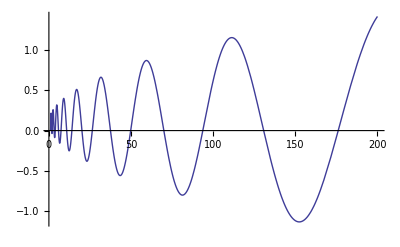

```mathematica
Plot[ag[n,10],{n,1,200}]
```

```mathematica
Integrate[ j^(-1/2)(2x Cos[x Log[j/n]]+Sin[x Log[j/n]]),{j,1,n}]
```

ConditionalExpression[-2 Sin[x Log[1/n]],Re[n]≥0||n∉Reals]

```mathematica
ag2[n_,x_]:=-2 Sin[x Log[1/n]]
```

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]+c],{j,1,n}]
```

ConditionalExpression[(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
ag3[n_,x_,c_]:=(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2)
ag3as[j_,x_,c_]:= j^(-1/2)Sin[x Log[j]+c]
ag3a[n_,x_,c_]:=(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2)-(Sin[c+x Log[n]]/(√n)+Sin[c])/2
```

```mathematica
ag3as[1,x,c]
```

Sin[c]

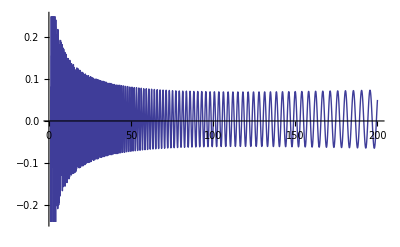

```mathematica
Plot[ag3a[n,N@Im@ZetaZero@100,0],{n,1,200}]
```

```mathematica
ag4[n_,x_,c_]:=Sum[ j^(-1/2)Sin[x Log[j]+c],{j,2,n}]
```

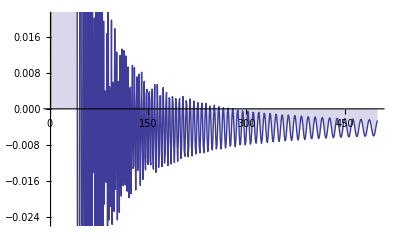

```mathematica
DiscretePlot[{ag4[n-1,N@Im@ZetaZero@100,0]-ag3a[n,N@Im@ZetaZero@100,0]},{n,1,500}]
```

```mathematica
Integrate[ j^(-1/2)(2x Cos[x Log[j/n]]+Sin[x Log[j/n]]),{j,0,n}]
```

ConditionalExpression[0 Sin[x (-∞)],-1/2<Im[x]<1/2]

```mathematica
Integrate[ j^(-1/2)(2x Cos[x Log[j/n]]+Sin[x Log[j/n]]),j]
```

2 √j Sin[x Log[j/n]]

```mathematica
FullSimplify[D[j^(-1/2)Sin[x Log[j]+c],{j,0}]]
```

Sin[c+x Log[j]]/(√j)

```mathematica
FullSimplify[D[j^(-1/2)Sin[x Log[j]+c],{j,1}]]
```

-(-2 x Cos[c+x Log[j]]+Sin[c+x Log[j]])/(2 j^(3/2))

```mathematica
FullSimplify[D[j^(-1/2)Sin[x Log[j]+c],{j,2}]]
```

(-8 x Cos[c+x Log[j]]+(3-4 x^2) Sin[c+x Log[j]])/(4 j^(5/2))

```mathematica
FullSimplify[D[j^(-1/2)Sin[x Log[j]+c],{j,3}]]
```

((46 x-8 x^3) Cos[c+x Log[j]]+3 (-5+12 x^2) Sin[c+x Log[j]])/(8 j^(7/2))

```mathematica
FullSimplify[D[j^(-1/2)Sin[x Log[j]+c],{j,4}]]
```

(32 x (-11+4 x^2) Cos[c+x Log[j]]+(105-344 x^2+16 x^4) Sin[c+x Log[j]])/(16 j^(9/2))

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]+c],j]
```

-(2 √j (2 x Cos[c+x Log[j]]-Sin[c+x Log[j]]))/(1+4 x^2)

```mathematica
Limit[-(2 √j (2 x Cos[c+x Log[j]]-Sin[c+x Log[j]]))/(1+4 x^2),j->0]
```

0

```mathematica
-(2 √j (2 x Cos[c+x Log[j]]-Sin[c+x Log[j]]))/(1+4 x^2)/.j->n
```

-(2 √n (2 x Cos[c+x Log[n]]-Sin[c+x Log[n]]))/(1+4 x^2)

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]+c],{j,1,n}]
```

ConditionalExpression[(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
FullSimplify[Integrate[ j^(-1/2)(2x Cos[x Log[j/(n+1)]]+Sin[x Log[j/(n+1)]]),{j,1,n+1}]-( ((n+1)^(-1/2)(2x Cos[x Log[(n+1)/(n+1)]]+Sin[x Log[(n+1)/(n+1)]]))+(1^(-1/2)(2x Cos[x Log[1/(n+1)]]+Sin[x Log[1/(n+1)]])))/2]
```

ConditionalExpression[-x/(√(1+n))-x Cos[x Log[1/(1+n)]]-5/2 Sin[x Log[1/(1+n)]],Re[n]≥-1||n∉Reals]

```mathematica
p[n_,x_]:=-x/(√(1+n))-x Cos[x Log[1/(1+n)]]-5/2 Sin[x Log[1/(1+n)]]
```

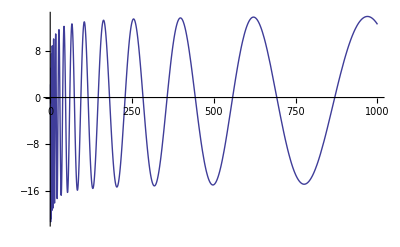

```mathematica
Plot[p[n,Im@ZetaZero@1],{n,1,1000}]
```

```mathematica
2 √j Sin[x Log[j/n]]/.j->0
```

0 Sin[x (-∞)]

```mathematica
FullSimplify[Sum[ j^(-1/2)Sin[x j+c],{j,1,n}]]
```

-1/2 ⅈ ⅇ^(-ⅈ (c+x+n x)) (LerchPhi[ⅇ^(-ⅈ x),1/2,1+n]-ⅇ^(2 ⅈ (c+x+n x)) LerchPhi[ⅇ^(ⅈ x),1/2,1+n]+ⅇ^(ⅈ (1+n) x) (-PolyLog[1/2,ⅇ^(-ⅈ x)]+ⅇ^(2 ⅈ c) PolyLog[1/2,ⅇ^(ⅈ x)]))

```mathematica
Sum[ j^(-1/2)Sin[x j+c],{j,1,Infinity}]
```

-1/2 ⅈ ⅇ^(-ⅈ c) (-PolyLog[1/2,ⅇ^(-ⅈ x)]+ⅇ^(2 ⅈ c) PolyLog[1/2,ⅇ^(ⅈ x)])

```mathematica
Sum[1/j  Sin[x j+c],{j,1,n}]
```

1/2 ⅈ ⅇ^(-ⅈ c-ⅈ x) (-(ⅇ^(-ⅈ x))^n LerchPhi[ⅇ^(-ⅈ x),1,1+n]+ⅇ^(2 ⅈ c+2 ⅈ x) (ⅇ^(ⅈ x))^n LerchPhi[ⅇ^(ⅈ x),1,1+n]+ⅇ^(2 ⅈ c+ⅈ x) Log[1-ⅇ^(ⅈ x)]-ⅇ^(ⅈ x) Log[ⅇ^(-ⅈ x) (-1+ⅇ^(ⅈ x))])

```mathematica
FullSimplify@Integrate[j^(-1/2) Sin[x j+c],{j,1,n}]
```

ConditionalExpression[(√(2 π) (Cos[c] (-FresnelS[√(2/π) √x]+FresnelS[√n √(2/π) √x])+(-FresnelC[√(2/π) √x]+FresnelC[√n √(2/π) √x]) Sin[c]))/(√x),Re[n]≥0||n∉Reals]

```mathematica
Integrate[ j^(-1/2)Sin[x j+c],{j,1,Infinity}]
```

(√(π/2) (x (x^2)^(1/4) Cos[c]+(x^2)^(3/4) Sin[c]-2 x^(3/2) (Cos[c] FresnelS[√(2/π) √x]+FresnelC[√(2/π) √x] Sin[c])))/x^2

```mathematica
Integrate[ j^(-1)Sin[x j+c],{j,1,Infinity}]
```

(π √(x^2) Cos[c])/(2 x)-CosIntegral[x] Sin[c]+Log[x] Sin[c]-1/2 Log[x^2] Sin[c]-Cos[c] SinIntegral[x]

```mathematica
Integrate[ j^(-1)Sin[x j+c],{j,1,Infinity}]
```

```mathematica
cp[n_,x_,c_]:=-1/2 ⅈ ⅇ^(-ⅈ (c+x+n x)) (LerchPhi[ⅇ^(-ⅈ x),1/2,1+n]-ⅇ^(2 ⅈ (c+x+n x)) LerchPhi[ⅇ^(ⅈ x),1/2,1+n]+ⅇ^(ⅈ (1+n) x) (-PolyLog[1/2,ⅇ^(-ⅈ x)]+ⅇ^(2 ⅈ c) PolyLog[1/2,ⅇ^(ⅈ x)]))
cp2[n_,x_,c_]:=(√(2 π) (Cos[c] (-FresnelS[√(2/π) √x]+FresnelS[√n √(2/π) √x])+(-FresnelC[√(2/π) √x]+FresnelC[√n √(2/π) √x]) Sin[c]))/(√x)
```

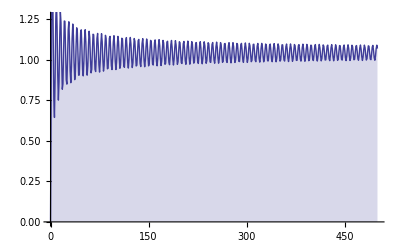

```mathematica
DiscretePlot[ Re@cp[n,1,0],{n,0,500}]
```

```mathematica
FullSimplify[Sum[ j^(-1/2)Sinh[Log[x] j+Log[c]],{j,1,Infinity}]]/.c->1
```

-1/2 PolyLog[1/2,1/x]+1/2 PolyLog[1/2,x]

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]+c],{j,1,n}]
```

ConditionalExpression[(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
FullSimplify[D[(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2)-(Sin[c+x Log[n]]/(√n)+Sin[c])/2,n]/.c->0]
```

(-2 x Cos[x Log[n]]+(1+4 n) Sin[x Log[n]])/(4 n^(3/2))

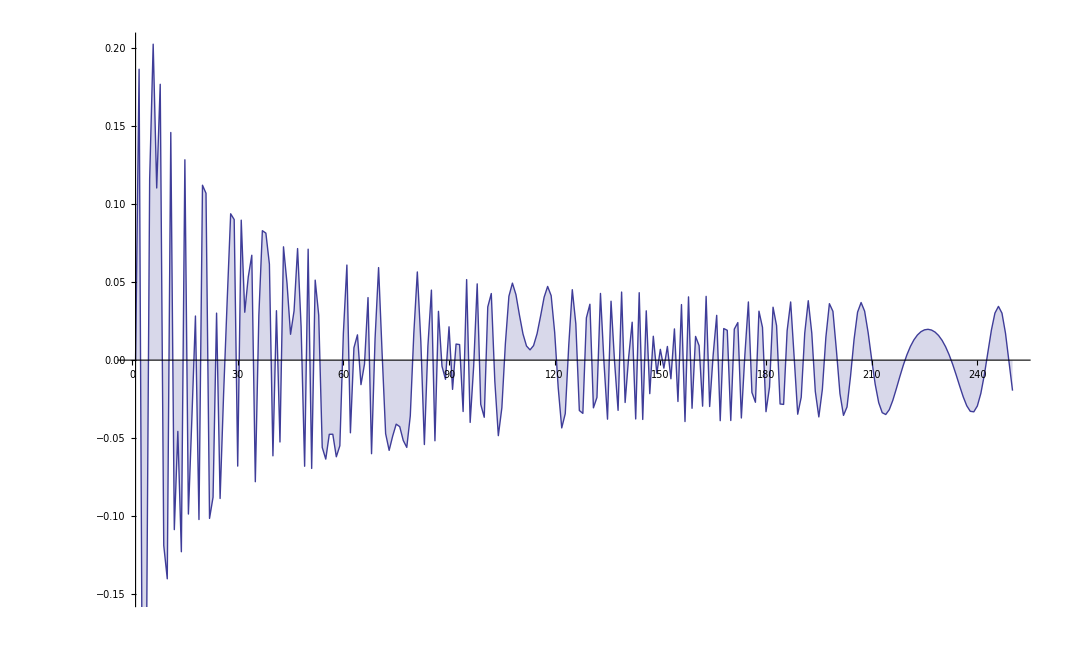

```mathematica
DiscretePlot[(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2)-(Sin[c+x Log[n]]/(√n)+Sin[c])/2/.c->0/.x->1419.4224809459956,{n,1,250}]
```

```mathematica
1/j^x
```

j^-x

```mathematica
FullSimplify@Sum[ 2(-1)^(j+1) j^(-1/2)Sinh[x Log[j]],{j,1,n}]
```

2^(-1/2-x) (Zeta[1/2+x]+4^x (-Zeta[1/2-x]+Zeta[1/2-x,3/2]+(-1)^n (-Zeta[1/2-x,(1+n)/2]+Zeta[1/2-x,(2+n)/2]))-Zeta[1/2+x,3/2]+(-1)^n Zeta[1/2+x,(1+n)/2]-(-1)^n Zeta[1/2+x,(2+n)/2])

```mathematica
2^(-1/2-x) (Zeta[1/2+x]+4^x (-Zeta[1/2-x]+Zeta[1/2-x,3/2]+(-1)^n (-Zeta[1/2-x,(1+n)/2]+Zeta[1/2-x,(2+n)/2]))-Zeta[1/2+x,3/2]+(-1)^n Zeta[1/2+x,(1+n)/2]-(-1)^n Zeta[1/2+x,(2+n)/2])/.x->14.134725141734695I/.n->10000000000.0
```

2.17031×10^-11+9.52564×10^-6 ⅈ

```mathematica
N@ZetaZero@1
```

0.5+14.1347 ⅈ

```mathematica
so[n_,x_]:=Sum[ 2(-1)^(j+1) j^(-1/2)Sin[x Log[j]],{j,1,n}]
```

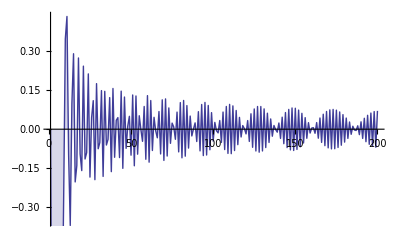

```mathematica
DiscretePlot[so[n,Im@ZetaZero@2],{n,1,200}]
```

```mathematica
{((1-2^(1/2-x))^-1),((1-2^(1/2+x))^-1)}
```

{1/(1-2^(1/2-x)),1/(1-2^(1/2+x))}

```mathematica
FullSimplify[((1-2^(1/2-x))^-1) /(2^(-1/2))]
```

√2+2/(-√2+2^x)

```mathematica
j^(-1/2)(((1-2^(1/2-x))^-1)((-1)^(j+1)/j^x)-((1-2^(1/2+x))^-1)((-1)^(j+1)/j^-x))
```

(((-1)^(1+j) j^-x)/(1-2^(1/2-x))-((-1)^(1+j) j^x)/(1-2^(1/2+x)))/(√j)

```mathematica
FullSimplify[(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2)]
```

(4 x Cos[c]-2 Sin[c]+2 √n (-2 x Cos[c+x Log[n]]+Sin[c+x Log[n]]))/(1+4 x^2)

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]],j]
```

(2 √j (-2 x Cos[x Log[j]]+Sin[x Log[j]]))/(1+4 x^2)

```mathematica
(Integrate[ j^(-1/2)Sin[x Log[j]+c],j]/.j->n)-(Integrate[ j^(-1/2)Sin[x Log[j]+c],j]/.j->1)
```

(2 (2 x Cos[c]-Sin[c]))/(1+4 x^2)-(2 √n (2 x Cos[c+x Log[n]]-Sin[c+x Log[n]]))/(1+4 x^2)

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]+C],{j,1,n+1}]
```

ConditionalExpression[(4 x Cos[C]-2 Sin[C]+2 √(1+n) (-2 x Cos[C+x Log[1+n]]+Sin[C+x Log[1+n]]))/(1+4 x^2),Re[n]≥-1||n∉Reals]

```mathematica
Integrate[ j^(-1/2)Sin[x Log[j]],j]/.j->n
```

(2 √n (-2 x Cos[x Log[n]]+Sin[x Log[n]]))/(1+4 x^2)

```mathematica
Integrate[ j^(-1/2)Cos[x Log[j]],{j,1,n}]
```

ConditionalExpression[(-2+2 √n (Cos[x Log[n]]+2 x Sin[x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
ff[j_,x_]:=j^(-1/2)Sin[x Log[j]]
```

```mathematica
Sum[ ff[j,x],{j,1,b}]
```

∑_(j=1)^b Sin[x Log[j]]/(√j)

```mathematica
Integrate[ ff[j,x],{j,a,b}]+(ff[b,x]+ff[a,x])/2
```

ConditionalExpression[1/2 (Sin[x Log[a]]/(√a)+Sin[x Log[b]]/(√b))+(4 √a x Cos[x Log[a]]-2 √a Sin[x Log[a]]+2 √b (-2 x Cos[x Log[b]]+Sin[x Log[b]]))/(1+4 x^2),((Im[a]≥Im[b]&&Im[b] Re[a]≤Im[a] Re[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Im[a]≤Im[b]))&&((Re[a/(-a+b)]≥0&&a^2≠a b)||a/(a-b)∉Reals||Re[a/(a-b)]≥1)]

```mathematica
fr[x_,a_,b_]:=1/2 (Sin[x Log[a]]/(√a)+Sin[x Log[b]]/(√b))+(4 √a x Cos[x Log[a]]-2 √a Sin[x Log[a]]+2 √b (-2 x Cos[x Log[b]]+Sin[x Log[b]]))/(1+4 x^2)
frs[x_,a_,b_]:=Sum[ ff[j,x],{j,a,b}]
```

```mathematica
fr[x,1,n]
```

Sin[x Log[n]]/(2 √n)+(4 x+2 √n (-2 x Cos[x Log[n]]+Sin[x Log[n]]))/(1+4 x^2)

```mathematica
N@fr[20,1,20]
```

0.241714

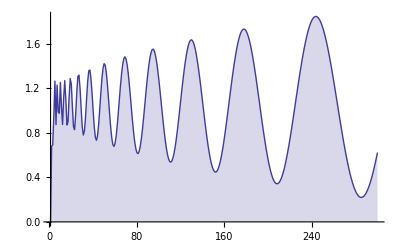

```mathematica
DiscretePlot[frs[20,1,n],{n,1,300}]
```

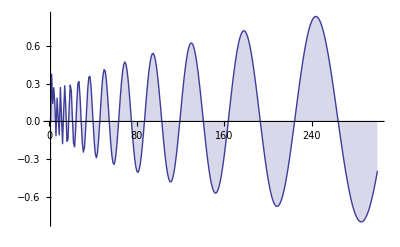

```mathematica
DiscretePlot[fr[20,1,n],{n,1,300}]
```

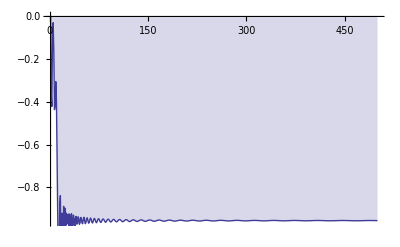

```mathematica
DiscretePlot[frs[70,1,n]-fr[70,1,n],{n,1,500}]
```

```mathematica
ff2[j_,x_,c_]:=j^(-1/2)Sin[x Log[j]+c]
fr2[x_,a_,b_,c_]:=1/2 (Sin[c+x Log[a]]/(√a)+Sin[c+x Log[b]]/(√b))+(4 √a x Cos[c+x Log[a]]-2 √a Sin[c+x Log[a]]+2 √b (-2 x Cos[c+x Log[b]]+Sin[c+x Log[b]]))/(1+4 x^2)
frs2[x_,a_,b_,c_]:=Sum[ ff2[j,x,c],{j,a,b}]
```

```mathematica
Integrate[ ff2[j,x,c],{j,a,b}]+(ff2[b,x,c]+ff2[a,x,c])/2
```

ConditionalExpression[1/2 (Sin[c+x Log[a]]/(√a)+Sin[c+x Log[b]]/(√b))+(4 √a x Cos[c+x Log[a]]-2 √a Sin[c+x Log[a]]+2 √b (-2 x Cos[c+x Log[b]]+Sin[c+x Log[b]]))/(1+4 x^2),((Im[a]≥Im[b]&&Im[b] Re[a]≤Im[a] Re[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Im[a]≤Im[b]))&&((Re[a/(-a+b)]≥0&&a^2≠a b)||a/(a-b)∉Reals||Re[a/(a-b)]≥1)]

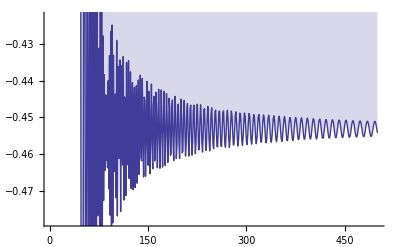

```mathematica
DiscretePlot[frs2[N@Im@ZetaZero@120,1,n,2]-fr2[N@Im@ZetaZero@120,1,n,2],{n,1,500}]
```

```mathematica
(D[ff2[b,x,c],{b,2}]-D[ff2[a,x,c],{a,2}])/12
```

1/12 ((x Cos[c+x Log[a]])/a^(5/2)-(x Cos[c+x Log[b]])/b^(5/2)-(3 Sin[c+x Log[a]])/(4 a^(5/2))-(-(x Cos[c+x Log[a]])/a^2-(x^2 Sin[c+x Log[a]])/a^2)/(√a)+(3 Sin[c+x Log[b]])/(4 b^(5/2))+(-(x Cos[c+x Log[b]])/b^2-(x^2 Sin[c+x Log[b]])/b^2)/(√b))

```mathematica
N[ZetaZero[1000]]
```

0.5+1419.42 ⅈ

```mathematica
FullSimplify@Integrate[ j^(-1/2) Sin[ x Log[a j]],{j,1,n}]
```

ConditionalExpression[(4 x Cos[x Log[a]]-2 Sin[x Log[a]]+2 √n (-2 x Cos[x Log[a n]]+Sin[x Log[a n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
ff4[j_,x_,c_]:=j^(-1/2)Sin[x Log[c j]]
fr4[x_,a_,b_,c_]:=1/2 (Sin[x Log[a c]]/(√a)+Sin[x Log[b c]]/(√b))+(4 √a x Cos[x Log[a c]]-2 √a Sin[x Log[a c]]+2 √b (-2 x Cos[x Log[b c]]+Sin[x Log[b c]]))/(1+4 x^2)
frs4[x_,a_,b_,c_]:=Sum[ ff4[j,x,c],{j,a,b}]
```

```mathematica
Integrate[ ff4[j,x,c],{j,a,b}]+(ff4[b,x,c]+ff4[a,x,c])/2
```

ConditionalExpression[1/2 (Sin[x Log[a c]]/(√a)+Sin[x Log[b c]]/(√b))+(4 √a x Cos[x Log[a c]]-2 √a Sin[x Log[a c]]+2 √b (-2 x Cos[x Log[b c]]+Sin[x Log[b c]]))/(1+4 x^2),((Im[a]≥Im[b]&&Im[b] Re[a]≤Im[a] Re[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Im[a]≤Im[b]))&&((Re[a/(-a+b)]≥0&&a^2≠a b)||a/(a-b)∉Reals||Re[a/(a-b)]≥1)]

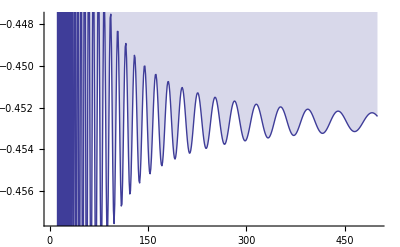

```mathematica
DiscretePlot[frs4[N@Im@ZetaZero@12,1,n,.1]-fr4[N@Im@ZetaZero@12,1,n,.1],{n,1,500}]
```

```mathematica
FullSimplify[fr4[x,1,n,c]]/.c->a
```

1/2 (Sin[x Log[a]]+Sin[x Log[a n]]/(√n))+(4 x Cos[x Log[a]]-2 Sin[x Log[a]]+2 √n (-2 x Cos[x Log[a n]]+Sin[x Log[a n]]))/(1+4 x^2)

1/2 (Sin[c]+Sin[c+x Log[a]]/(√a))+(4 √a x Cos[c+x Log[a]]+2 (-2 x Cos[c]+Sin[c])-2 √a Sin[c+x Log[a]])/(1+4 x^2)

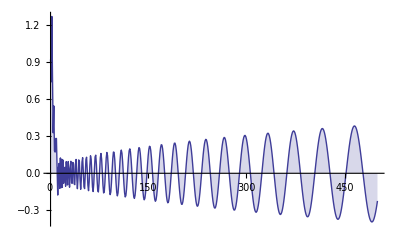

```mathematica
DiscretePlot[frs4[N@Im@ZetaZero@12,1,n,.1],{n,1,500}]
```

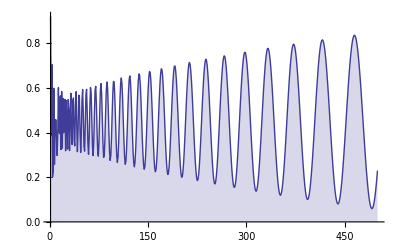

```mathematica
DiscretePlot[fr4[N@Im@ZetaZero@12,1,n,.1],{n,1,500}]
```

```mathematica
FullSimplify[1/2 (Sin[x Log[a]]+Sin[x Log[a n]]/(√n))+(4 x Cos[x Log[a]]-2 Sin[x Log[a]]+2 √n (-2 x Cos[x Log[a n]]+Sin[x Log[a n]]))/(1+4 x^2)]
```

1/2 (Sin[x Log[a]]+Sin[x Log[a n]]/(√n))+(4 x Cos[x Log[a]]-2 Sin[x Log[a]]+2 √n (-2 x Cos[x Log[a n]]+Sin[x Log[a n]]))/(1+4 x^2)